# Parâmetros nu - fit 2024 ( Near Detector )

## T[1][2] (T_μτ) : Plots χ^2(var) - One variable only

## 2_Reducing a list of 2 variables to 1 : { Var, Var2, χ^2 } → { Var, χ^2 }

```mathematica
Red2for1[Inlist_, Var_, Var2_]:=
Module[{tab,lis,nunN,nun3,newlisOne,list,nun,nun2,newlis,NewlisOne},
(* Código da função *)
list=Inlist;

(* Creating the list: { Var, χ^2 } *)
nun={};nun2={};
tab=Table[{list[[i,Var]],list[[i,Var2]],list[[i,3]]},{i,Length@list}];
lis=tab[[Ordering@PadRight@tab]]; 
If[Var==1,
Do[
	If[ Length[nun]== 0,If[lis[[1,Var]]≠ lis[[i,Var]],AppendTo[nun,i]] ]
,{i,Length@lis}];
Do[
	If[ Length[nun2]== 0,If[lis[[1,Var2]]≠ lis[[i,Var2]],AppendTo[nun2,i]] ]
,{i,Length@lis}];
,
Do[
	If[ Length[nun]== 0,If[lis[[1,Var2]]≠ lis[[i,Var2]],AppendTo[nun,i]] ]
,{i,Length@lis}];
Do[
	If[ Length[nun2]== 0,If[lis[[1,Var]]≠ lis[[i,Var]],AppendTo[nun2,i]] ]
,{i,Length@lis}];
];
nunN=(nun-{1})/(nun2-{1});
nun2=nun2-{1};
nun3=(Length@lis)/(nunN*nun2);

newlisOne=Table[
{
 lis[[1+i*nunN[[1]],1]],
Min[ lis[[1+i*nunN[[1]]*nun2[[1]];;(1+i)*nunN[[1]],3]] ]
 }
,{i,0,nun3[[1]]-1}];


(* Return: *)
NewlisOne=newlisOne
]
```

## With BG (9000): ϵ_μτ

### For ϵ_μτ:

```mathematica
(*pathImpor="/home/edson/Projeto_doutorado/Experimentos/Beam_Tau/DUNE_py/NSI_02_DUNE/my_data_2D/";*)
pathImpor=NotebookDirectory[];

text = "DUNE_Near9000_NSI_fit2D_WithBG_Eps_alpha";
list=Import[StringJoin[pathImpor,text]];
newlis=Red2for1[list, 1, 2];
newlis
Export["/home/edson/Projeto_doutorado/Experimentos/Beam_Tau/Table_DUNE_epsmut/Eps_Near_pos.dat",newlis]

textPi = "DUNE_Near9000_NSI_fit2D_WithBG_PiEps_alpha";
listPi=Import[StringJoin[pathImpor,textPi]];
newlisPi=Red2for1[listPi, 1, 2];
newlisPi
Export["/home/edson/Projeto_doutorado/Experimentos/Beam_Tau/Table_DUNE_epsmut/Eps_Near_min.dat",newlisPi]
```

{{0.,-1.2×10^-11},{5.×10^-6,0.00371382},{0.00001,0.0272978},{0.000015,0.0747212},{0.00002,0.145248},{0.000025,0.23832},{0.00003,0.353626},{0.000035,0.490983},{0.00004,0.650283},{0.000045,0.831458},{0.00005,1.03447},{0.000055,1.25928},{0.00006,1.5059},{0.000065,1.77431},{0.00007,2.06452},{0.000075,2.37653},{0.00008,2.71036},{0.000085,3.06604},{0.00009,3.44357},{0.000095,3.84298},{0.0001,4.26431},{0.000105,4.70757},{0.00011,5.17281},{0.000115,5.66004},{0.00012,6.16932},{0.000125,6.70068},{0.00013,7.25416},{0.000135,7.8298},{0.00014,8.42764},{0.000145,9.04774},{0.00015,9.69014},{0.000155,10.3549},{0.00016,11.042},{0.000165,11.7516},{0.00017,12.4838},{0.000175,13.2385},{0.00018,14.0158},{0.000185,14.8158},{0.00019,15.6386},{0.000195,16.4842},{0.0002,17.3526}}

/home/edson/Projeto_doutorado/Experimentos/Beam_Tau/Table_DUNE_epsmut/Eps_Near_pos.dat

{{0.,-1.2×10^-11},{5.×10^-6,0.00370895},{0.00001,0.027283},{0.000015,0.0746966},{0.00002,0.145214},{0.000025,0.238277},{0.00003,0.353573},{0.000035,0.490921},{0.00004,0.650212},{0.000045,0.831377},{0.00005,1.03438},{0.000055,1.25919},{0.00006,1.50579},{0.000065,1.77419},{0.00007,2.06439},{0.000075,2.37639},{0.00008,2.71022},{0.000085,3.06588},{0.00009,3.44341},{0.000095,3.84281},{0.0001,4.26413},{0.000105,4.70738},{0.00011,5.17261},{0.000115,5.65983},{0.00012,6.1691},{0.000125,6.70045},{0.00013,7.25392},{0.000135,7.82955},{0.00014,8.42738},{0.000145,9.04747},{0.00015,9.68986},{0.000155,10.3546},{0.00016,11.0417},{0.000165,11.7513},{0.00017,12.4835},{0.000175,13.2381},{0.00018,14.0155},{0.000185,14.8155},{0.00019,15.6382},{0.000195,16.4838},{0.0002,17.3523}}

/home/edson/Projeto_doutorado/Experimentos/Beam_Tau/Table_DUNE_epsmut/Eps_Near_min.dat

-1.2×10^-11

{{1}}

0.

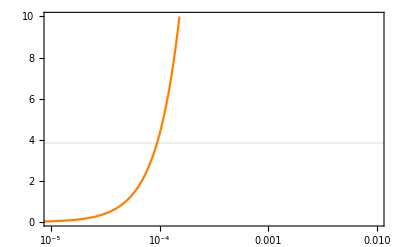

-1.2×10^-11

{{1}}

0.

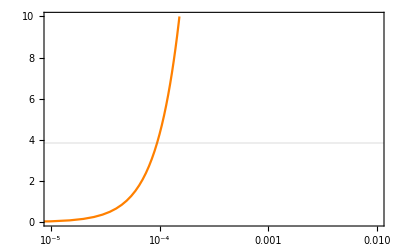

```mathematica
(* For ϵμτ positive *)
data = newlis;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];
min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]
(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListPlot[DataMin, Joined->True, PlotStyle->Orange,
ScalingFunctions->{"Log10",None},

PlotRange->{{10^-5,10^-2},{0,10}},Frame->True,GridLines->{{},{3.84}}]


(* For ϵμτ negative *)
dataPi = newlisPi;
xPi=Transpose[dataPi][[1]];
chi2Pi= Transpose[dataPi][[2]];
minPi=Min[chi2Pi]
posPi = Position[chi2Pi,minPi]
xminPi=xPi[[posPi[[1,1]]]]
(* Data_Plot *)
DataMinPi=Table[{xPi[[i]],chi2Pi[[i]]-minPi},{i,1,Length[xPi]}];
PlotChi2NOPi=ListPlot[DataMinPi, Joined->True, PlotStyle->Orange,
ScalingFunctions->{"Log10",None},

PlotRange->{{10^-5,10^-2},{0,10}},Frame->True,GridLines->{{},{3.84}}]
```

### For α:

```mathematica
(*pathImpor="/home/edson/Projeto_doutorado/Experimentos/Beam_Tau/DUNE_py/NSI_02_DUNE/my_data_2D/";*)
pathImpor=NotebookDirectory[];

text = "DUNE_Near9000_NSI_fit2D_WithBG_Eps_alpha";
list=Import[StringJoin[pathImpor,text]];
newlis=Red2for1[list, 2, 1];
newlis

textPi = "DUNE_Near9000_NSI_fit2D_WithBG_PiEps_alpha";
listPi=Import[StringJoin[pathImpor,textPi]];
newlisPi=Red2for1[listPi, 2, 1];
newlisPi
```

{{-0.01,187.656},{-0.0095,169.303},{-0.009,151.9},{-0.0085,135.445},{-0.008,119.939},{-0.0075,105.38},{-0.007,91.7667},{-0.0065,79.0989},{-0.006,67.3753},{-0.0055,56.595},{-0.005,46.7571},{-0.0045,37.8605},{-0.004,29.9045},{-0.0035,22.888},{-0.003,16.81},{-0.0025,11.6697},{-0.002,7.46614},{-0.0015,4.1983},{-0.001,1.86529},{-0.0005,0.466167},{0.,-1.2×10^-11},{0.0005,0.465856},{0.001,1.8628},{0.0015,4.18991},{0.002,7.44626},{0.0025,11.6309},{0.003,16.7429},{0.0035,22.7814},{0.004,29.7454},{0.0045,37.6341},{0.005,46.4464},{0.0055,56.1815},{0.006,66.8384},{0.0065,78.4163},{0.007,90.9142},{0.0075,104.331},{0.008,118.666},{0.0085,133.919},{0.009,150.088},{0.0095,167.172},{0.01,185.171}}

{{-0.01,187.656},{-0.0095,169.303},{-0.009,151.9},{-0.0085,135.445},{-0.008,119.939},{-0.0075,105.38},{-0.007,91.7667},{-0.0065,79.0989},{-0.006,67.3753},{-0.0055,56.595},{-0.005,46.7571},{-0.0045,37.8605},{-0.004,29.9045},{-0.0035,22.888},{-0.003,16.81},{-0.0025,11.6697},{-0.002,7.46614},{-0.0015,4.1983},{-0.001,1.86529},{-0.0005,0.466167},{0.,-1.2×10^-11},{0.0005,0.465856},{0.001,1.8628},{0.0015,4.18991},{0.002,7.44626},{0.0025,11.6309},{0.003,16.7429},{0.0035,22.7814},{0.004,29.7454},{0.0045,37.6341},{0.005,46.4464},{0.0055,56.1815},{0.006,66.8384},{0.0065,78.4163},{0.007,90.9142},{0.0075,104.331},{0.008,118.666},{0.0085,133.919},{0.009,150.088},{0.0095,167.172},{0.01,185.171}}

-1.2×10^-11

{{21}}

0.

-1.2×10^-11

{{21}}

0.

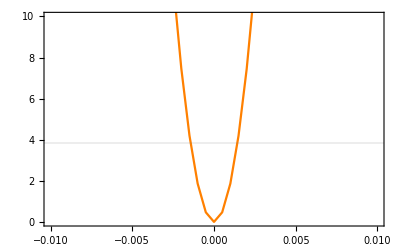

-Graphics-

```mathematica
(* For ϵμτ positive *)
data = newlis;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];
min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]
(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListPlot[DataMin, Joined->True, PlotStyle->Orange];


(* For ϵμτ negative *)
dataPi = newlisPi;
xPi=Transpose[dataPi][[1]];
chi2Pi= Transpose[dataPi][[2]];
minPi=Min[chi2Pi]
posPi = Position[chi2Pi,minPi]
xminPi=xPi[[posPi[[1,1]]]]
(* Data_Plot *)
DataMinPi=Table[{xPi[[i]],chi2Pi[[i]]-minPi},{i,1,Length[xPi]}];
PlotChi2NOPi=ListPlot[DataMinPi, Joined->True, PlotStyle->Orange];


(* With BG *)
plotWithoutBG=
Show[{PlotChi2NO},PlotRange->{0,10},Frame->True,GridLines->{{},{3.84}}]
plotWithoutBGPi=
Show[{PlotChi2NOPi},PlotRange->{0,10},Frame->True,GridLines->{{},{3.84}}]
```